# Random Walks

## Random Walk in 1 Dimension

```mathematica
randomWalk1D = Table[NestList[# + RandomChoice[{-1,1}]&,0,500],5000];
```

```mathematica
ListLinePlot[randomWalk1D]
```

-Graphics-

```mathematica
position = Map[#[[Length[#]]]& ,randomWalk1D];
```

```mathematica
meanPosition = Mean[position]
standardDeviationPosition = N[StandardDeviation[position]]
```

49/2500

22.5052

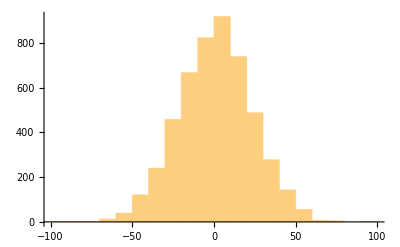

```mathematica
Histogram[position]
```

```mathematica
distances = Map[Abs[#[[Length[#]]]]& ,randomWalk1D];
```

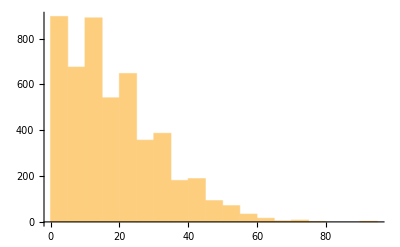

```mathematica
meanDistances = Mean[distances];
standardDeviationDistances= N[StandardDeviation[position]];
Histogram[distances]
```

## Random Walk in 2 Dimensions

```mathematica
ListLinePlot[Table[NestList[# + RandomChoice[{{1,0},{0,1},{0,-1},{-1,0}}]&,{0,0},500],1000]]
```

-Graphics-

## Random Walk in 3 Dimensions

```mathematica
ListLinePlot3D[Table[NestList[# + RandomChoice[{{1,0,0},{0,1,0},{0,-1,0},{-1,0,0},{0,0,1},{0,0,-1}}]&,{0,0,0},100],1000]]
```

-Graphics3D-